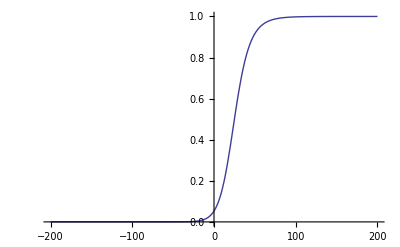

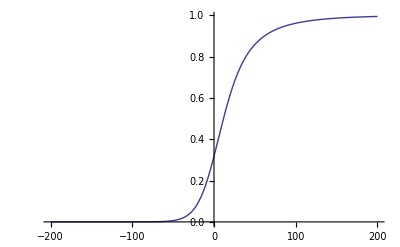

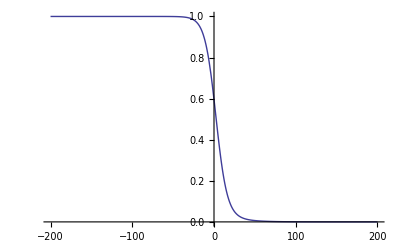

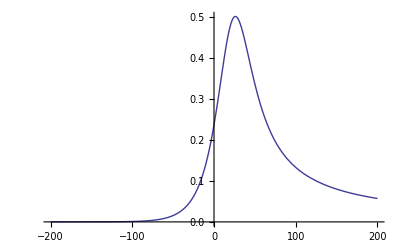

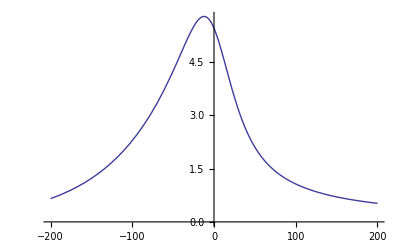

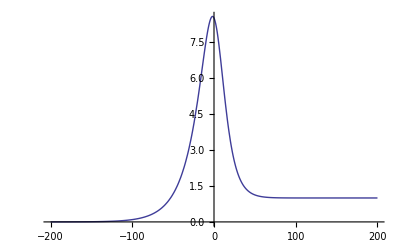

```mathematica
alpham[V_]:=(
0.1(25-V)/((E^((25-V)/10)) - 1)
)
betham[V_]:=(
4E^(-V/18)
)
alphah[V_]:=(
0.07E^(-V/20)
)
bethah[V_]:=(
1/((E^((30-V)/10))+1)
)
alphan[V_]:=(
(0.01(10-V))/((E^((10-V)/10))-1)
)
bethan[V_]:=(
0.125E^(-V/80)
)
m0[V_]:=(
alpham[V]/(alpham[V]+betham[V])
)
h0[V_]:=(
alphah[V]/(alphah[V]+bethah[V])
)
n0[V_]:=(
alphan[V]/(alphan[V]+bethan[V])
)
thaum[V_]:=(
1/(alpham[V]+betham[V])
)
thauh[V_]:=(
1/(alphah[V]+bethah[V])
)
thaun[V_]:=(
1/(alphan[V]+bethan[V])
)

Plot[m0[i],{i,-200,200}]
Plot[n0[i],{i,-200,200}]
Plot[h0[i],{i,-200,200}]
Plot[thaum[i],{i,-200,200}]
Plot[thaun[i],{i,-200,200}]
Plot[thauh[i],{i,-200,200},PlotRange->All]
```